1

1

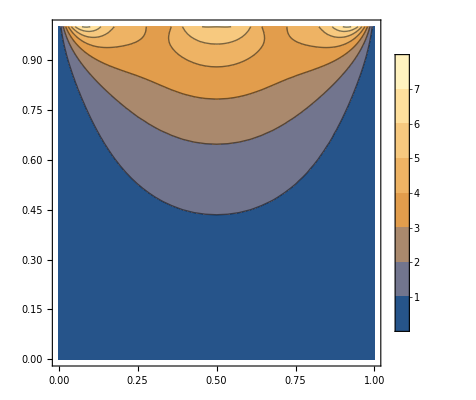

```mathematica
a = 1
b = 1
f1[x_, y_] := 20/(Pi*1*Sinh[Pi*1*b/a])*Sin[Pi*1*x/a]*Sinh[Pi*1*y/a]
f2[x_, y_] := 20/(Pi*3*Sinh[Pi*3*b/a])*Sin[Pi*3*x/a]*Sinh[Pi*3*y/a]
f3[x_, y_] := 20/(Pi*5*Sinh[Pi*5*b/a])*Sin[Pi*5*x/a]*Sinh[Pi*5*y/a]
f4[x_, y_] := 20/(Pi*7*Sinh[Pi*7*b/a])*Sin[Pi*7*x/a]*Sinh[Pi*7*y/a]
f5[x_, y_] := 20/(Pi*9*Sinh[Pi*9*b/a])*Sin[Pi*9*x/a]*Sinh[Pi*9*y/a]
f6[x_, y_] := 20/(Pi*11*Sinh[Pi*11*b/a])*Sin[Pi*11*x/a]*Sinh[Pi*11*y/a]
ContourPlot[{f1[x,y]+f2[x,y]+ f3[x,y]+f3[x,y]+f4[x,y]+f5[x,y]+f6[x,y]}, {x, 0 ,a}, {y, 0, b}, PlotLegends->Automatic]
```